```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;
K2meV=1000*8.617332478*10^−5;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesC={"C_4685_760.eV","C_4730_1900.eV","C_4759_2500.eV","C_4801_3200.eV","C_4850_3805.eV"};
filesZr={"Zr_4685_760.eV","Zr_4730_1900.eV","Zr_4759_2500.eV","Zr_4801_3200.eV","Zr_4850_3805.eV"};
(* old uses 2 data points for harmonic approximation:
filesCh={"harm.C_4685_760","harm.C_4730_1900","harm.C_4759_2500","harm.C_4801_3200","harm.C_4850_3805"};
filesZrh={"harm.Zr_4685_760","harm.Zr_4730_1900","harm.Zr_4759_2500","harm.Zr_4801_3200","harm.Zr_4850_3805"};
*)
(*New harmonic is only bases on a single displacement of 0.01 Angstrom for both Zr and C:*)
filesCh={"1.harm.C_4685_760.eV","1.harm.C_4730_1900.eV","1.harm.C_4759_2500.eV","1.harm.C_4801_3200.eV","1.harm.C_4850_3805.eV"};
filesZrh={"1.harm.Zr_4685_760.eV","1.harm.Zr_4730_1900.eV","1.harm.Zr_4759_2500.eV","1.harm.Zr_4801_3200.eV","1.harm.Zr_4850_3805.eV"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,5}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,5}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,5}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,5}];
```

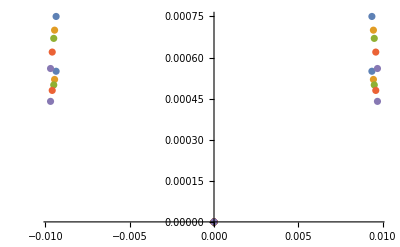

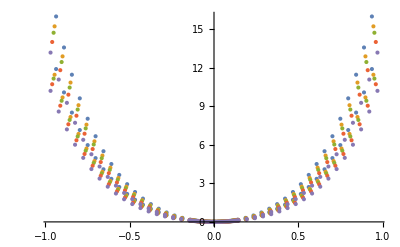

```mathematica
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

```mathematica
Define and fit potentials;

(*Carbon*)
V[1,2,x_]:=Table[Fit[hCdata[[i]],{x^2},x],{i,1,5}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,5}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
(*Zirconium*)
V[2,2,x_]:=Table[Fit[hZrdata[[i]],{x^2},x],{i,1,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,5}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,5}]
```

```mathematica
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,5}]
cOmega0=Sqrt[2Acarbon/m[[1]]]
```

{6.26446,5.8106,5.52852,5.20833,4.67637}

{1.02135,0.983652,0.959479,0.93128,0.882441}

```mathematica
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,5}]
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

{8.54244,7.82196,7.40822,6.72743,5.95175}

{0.432764,0.414112,0.403011,0.384048,0.361229}

```mathematica
xOp[dim_]:=SparseArray[{Band[{1,2}]->#,Band[{2,1}]->#},{#,#}&@dim]&[Table[Sqrt[i],{i,dim-1}]/Sqrt[2]]

eKin[dim_]:=(1/2)* SparseArray[{Band[{1,1}]->Table[i-1/2,{i,dim}],Band[{1,3}]->#,Band[{3,1}]->#},{#,#}&@dim]&[Table[-Sqrt[i (i+1)/2],{i,dim-2}]/Sqrt[2]]
spectrum[n_,tolerance_: .00001][potential_,var_]/;PolynomialQ[potential,var]:=Module[{x,h,e,v,c=CoefficientList[potential,var],min=First@Check[Minimize[potential,var],Print["No absolute potential minimum found. Make sure the leading power has a positive coefficient!"];
Abort[],Minimize::natt]},FixedPoint[{#[[1]]+1,Eigenvalues[h=eKin[#[[1]]]+N[Sum[c[[i]] MatrixPower[xOp[#[[1]]],i-1],{i,2,Length[c]}]+(c[[1]]-min) IdentityMatrix[#[[1]]]],-n]}&,{n+1,2 Reverse@Range[n]-1},SameTest->(Max@Abs[#1[[2]]-#2[[2]]]<tolerance&)];
{e,v}=Reverse/@Eigensystem[h,-n];
{e+min,ψe/@v}]
Format[ψe[l_List]]:=ψe[Row[{"«",Length[l],"»"}]]
ψe[l_List][x_]:=1/(Pi^(1/4))Exp[-x^2/2] l.(1/Sqrt[2^# #!] HermiteH[#,x]&[Range[Length[l]]-1])

plotSpectrum[data_,potential_,{var_,min_,max_}]:=Show[Apply[Plot[Evaluate[#1+(Last[#1]-First[#1])/(2+Length[#1])/2 Through[#2[var]]],{var,min,max},Prolog->{Gray,Map[Line[{{min,#},{max,#}}]&,#1]},Frame->True]&,data],Plot[potential,{var,min,max}]]
```

```mathematica
s=NDEigensystem[-(1/(2))*u''[x]+x*x*u[x],u[x],{x,-4,4},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}]//Timing
```

{1.21522,{{0.707107,2.12132,3.53553},{InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x],InterpolatingFunction[{{-4., 4.}}, <>][x]}}}

```mathematica
s[[1]]
s[[1]]/(2*s[[1]][[1]])
```

{0.707107,2.12132,3.53553}

{0.5,1.5,2.5}

```mathematica
t=spectrum[5][(x*x ),x]//Timing
```

{0.000016,spectrum[5][x^2,x]}

```mathematica
t[[1]]
t[[1]]/(2*t[[1]][[1]])
```

{0.707107,2.12132,3.53553,4.94975,6.36396}

{0.5,1.5,2.5,3.5,4.5}